```mathematica
R1 =Exp[(x*x*x*x+x*x-x+(√5))/5]
```

ⅇ^(1/5 (√5-x+x^2+x^4))

```mathematica
R2=  Sinh[((x*x*x+21*x+9)/(21*x+6))];
```

```mathematica
NSolve[R1+R2-3==0,x]
```

$Aborted

```mathematica
FindRoot[R1+R2-3==0,{x,0.5}]
```

{x→0.485204}

```mathematica
0.48520424928660594
```

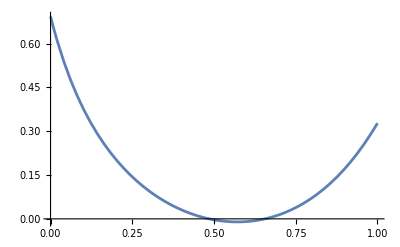

```mathematica
Plot[R1+R2-3,{x,0,1}]
```